# AD Implementation Forward Mode

The forward mode of AD is relatively simple to understand.  This is a brief review of gradients and Jacobians and how forward mode AD works.  Implementation details if time permits.

## Calculus 3 Review

### Partial and Directional Derivatives f:ℝ^n→ℝ

The partial derivative is defined analogously to the calculus one definition
	(∂f)/(∂x_j)=lim_(h→0) (f(x+h e_j)-f(x))/h
it is the slope in the j^th direction.  The directional derivative in the direction u is 
	(∂f)/(∂u)=lim_(h→0) (f(x+h u)-f(x))/h
Calculus 3 usually normalizes directions:  the definition makes sense for non-normalized vectors.  It is computationally better to compute with centered differences
	(∂f)/(∂u)=lim_(h→0) (f(x + h u)-f(x - h u ))/(2h)
Note that (∂f)/(∂x_i):ℝ^n→ℝ.

In calculus 3 you symbolically computed ∂f/∂x_1 by freezing the variables x_2 etc and using calculus one symbolic techniques to differentiate with respect to x_1.

### Gradients f:ℝ^n→ℝ

The gradient is simply the vector of partial derivatives
	∇f=((∂f)/(∂x_1),(∂f)/(∂x_2),… ,(∂f)/(∂x_n))
Note ∇f:ℝ^n→ℝ^n.

Interpretation:
The gradient points in the steepest direction uphill;
The gradient is perpendicular to level surfaces;
At a smooth minimum x of f  we have ∇f(x)=0;
…

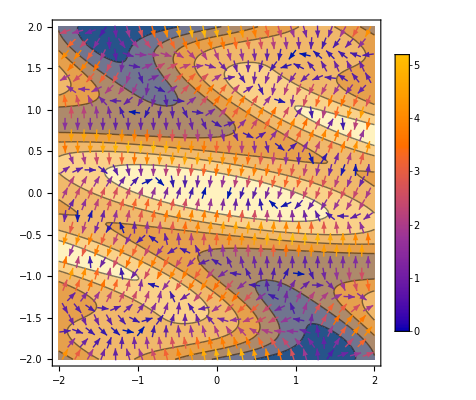

```mathematica
Clear[x1,x2,f,delf]
f[{x1_,x2_}]:= Sin[x1 x2 + Cos[x1+4 x2]]+Cos[x2]
delf[{x1_,x2_}]=D[f[{x1,x2}],{{x1,x2}}];
Show[
ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},PlotPoints->25],
VectorPlot[delf[{x1,x2}],{x1,-2,2},{x2,-2,2},VectorPoints->Fine,PlotLegends->Automatic]]
```

### Jacobians f:ℝ^n→ℝ^m

For a vector valued function you just differentiate the m component functions 		
	f=(f_1,f_2,…,f_m)
to get a matrix J (J is for Jacobian) with entries 
	J_(i,j)=(∂f_i)/(∂x_j)
Note: J:ℝ^n→ℝ^(m×n).  You can think of as either a stack of columns  
	J=((∂f)/(∂x_1) (∂f)/(∂x_2) … (∂f)/(∂x_n))
or a pile of rows
	J=(∇f_1
∇f_2
⋮
∇f_m)

In calculus 3 you used the determinant of the Jacobian to compute volume changes for 2D and 3D integrals.  In 2D this area transformation looked like
	dA=det((∂f_1)/(∂x) | (∂f_1)/(∂y)
(∂f_2)/(∂x) | (∂f_2)/(∂y))dx dy

## AD Idea

Computers really just do a lot of arithmetic and a little logic. Arithmetic is differentiable!  Computer program should be differentiable using the sum rule
	(u+v)'=u'+v'
and the product rule
	(u v)'=u'v+u v'.

The question is how to organize differentiating a computer program.  The easiest thing to do is to just include the derivative (using the rules up above) as you go.  You get the following simple extended addition and multiplication rules.  
	(u,du)+(v,dv)=(u+v,u'+v')
and the product rule
	(u, du) ×(v,dv)=(u×v, du×v+u×dv)

For a function of two variables f:ℝ^2→ℝ computing the extended f at the vector with first component (x_1,1)  and second component (x_2,0)  gives f and (∂f)/(∂x_1) at the point x. Computing the extended f at the vector with first component (x_1,0)  and second component (x_2,1)  gives f and (∂f)/(∂x_2) at the point x.  Forward mode AD is just making this process automatic.

## Finite Difference (FD) Approximations

Finite Difference approximations are much less accurate and need to be used with care.

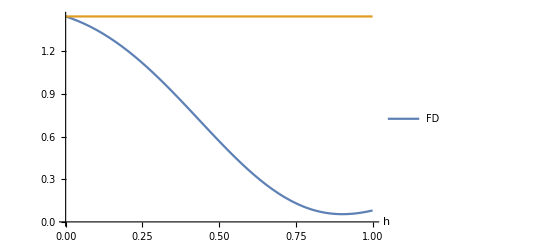

```mathematica
f[x_]:= Sin[x+ Sin[x^2]]
x0=0.5;
Plot[{(f[x0+h]-f[x0])/h,f'[x0]},{h,0,1},AxesLabel->{"h"},
PlotLegends->{"FD"}]
```

## Differentiating a Schur Decomposition

The Schur decomposition of a matrix A is 
	A=Q.T.Qᵀ or equivalently T=Qᵀ.A.Q
where Q is orthogonal (Q.Qᵀ=I) and T is upper triangular. Differentiating gives
	A'=Q'.T.Qᵀ+Q.T'.Qᵀ+Q.T.(Qᵀ)' 
and 
	Q'.Qᵀ+Q.(Qᵀ)'=0

```mathematica
m=4;
A=RandomReal[{-1,1},{m,m}];
{Q,T}=SchurDecomposition[A];
Map[Norm,{A-Q.T.Qᵀ,Q.Qᵀ}]
```

{3.97528×10^-15,1.}